#### Sezione F:

#### in questa Brutta sezione F mi sembra adeguato dimostrare il teorema di Sharkovskiy (Шарко́вський) facendo riferimento (come esempio specifico) alla mappa logistica

Th: sia · → · un ordine totale definito su ℕ nel seguente modo
3 →  5 →  7 →  9 →  11 →  ...      
→  3×2 →  5×2 →  7×2 → ...     
→ 3×2^2 →  5×2^2→  7×2^2→ ... 
→  3×2^n →  5×2^n→  7×2^n→ ...   
... →2^3 →  2^2 →  2 → 1
quest’ordine ha come supremo 3, come infimo 1

Il teorema di Sharkovskiy afferma che, data f:I→I una mappa continua, se f ha un punto periodico primitivo di periodo m→n allora possiede anche un punto periodico di periodo n

vogliamo dimostrare che, se esiste un’orbita di periodo 3 allora esistono orbite di ogni periodo
indi che esistono a,b,c ∈ ℝ t.c. f:a↦b↦c↦a

si utilizzano i seguenti fatti, data una funzione f continua

· teorema del punto fisso di Brouwer, ossia I⊆f(I) ⇒ f ha un p. fisso in I
· V ⊆ f(U) ⇒ ∃ U_0⊆U : V = f(U_0)

```mathematica
f[μ_,x_]:= μ x(1-x)
fn[μ_,x_,n_]:= Nest[f[μ,#]&,x,n]
```

```mathematica
D[f[μ,x],x]
```

(1-x) μ-x μ

(1 - x) μ - x μ  = μ(1-2x)= 0 ⇔ x=1/2 supponendo μ≠0

```mathematica
f[μ,1/2](*è il massimo*)
```

μ/4

f_μ:ℝ→[-∞,μ/4] ⊂ ℝ ergo valgono le ipotesi di cui sopra.

la mappa f_μ possiede un’orbita 3-periodica in una finestra regolare per μ>μ_∞ abbiamo trovato nei punti precedenti un tale μ (che chiameremo μ_p3 d’ora in avanti) e vale ≈3.8281, in realtà la mappa con orbite di periodo 3 vale circa da 3.828 a 3.841 quindi per comodità prendiamo μ_p3=3.835
ridefiniamo le funzioni per comodità

```mathematica
f3[x_]:=f[3.835,x]
fn3[x_,n_]:=fn[3.835,x,n]
```

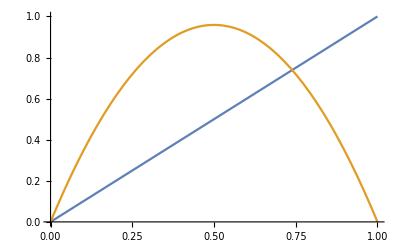

```mathematica
Plot[{x,f3[x]},{x,0,1}]
```

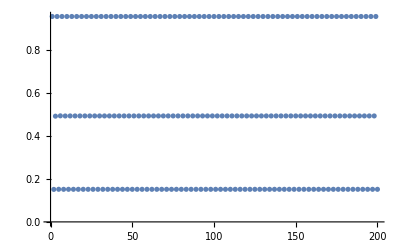

```mathematica
ListPlot[fn3[0.5,#]&/@Range[200]]
```

```mathematica
{a,b,c}= fn3[0.5,#]&/@{50,51,52}
I0={a,b};
I1={b,c};
(*50 iterazioni sono per stabilizzare eventuali convergenze*)
```

{0.152074,0.494514,0.958635}

Vogliamo dimostrare l’esistenza di un punto fisso (n=1)

```mathematica
{f3[a]==b,f3[b]==c}
```

{True,True}

⇒[a,c] ⊆f3(I_1) ⇒ (Brower) ∃ un punto fisso nell’interno di I_1
in effetti sappiamo che (μ - 1)/μ ≈

```mathematica
(3.835-1)/3.835
```

0.739244

è punto fisso (sempre) ed è interno a [b,c]

sia ora n>1, n≠3, vogliamo dimostrare l’esistenza di un’orbita di periodo n
per fare questo costruiamo J_n⊂...⊂ J_2⊂J_1⊂J_0=I_1
f(J_k)= J_(k-1) ∀k = 1 ... n-2
f^k(J_k)= I_1
f^(n-1)(J_(n-1))= I_0
f^n(J_n)= I_1

per costruire tale successione di intervalli possiamo usare l’antimmagine.
sappiamo che J_k= f^-1(J_(k-1)) e che tutte le orbite sono contenute in [0,1]